```mathematica
distanceCSV=Import["https://raw.githubusercontent.com/HALtheWise/POE-lab2/master/docs/zeroPassDistances.csv","Csv"];
distanceData=distanceCSV[[2;;Length[distanceCSV]-1]];
```

```mathematica
line = Fit[distanceData, {1,x,x^2,x^3},x]
Fit[Map[Reverse,distanceData], {1,x,x^2,x^3},x]
```

782.774-15.9408 x+0.128033 x^2-0.000356379 x^3

230.143-1.4452 x+0.00354446 x^2-2.93605×10^-6 x^3

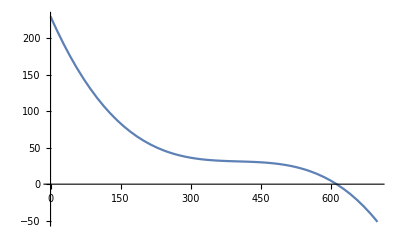

```mathematica
Plot[230.1430411867322-1.4451995839029892 x+0.0035444572391777783 x^2-2.9360497052173657*^-6 x^3,{x,0,700}]
```

```mathematica
voltageToDistance[x_]=(230.1430411867322-1.4451995839029892 x+0.0035444572391777783 x^2-2.9360497052173657*^-6 x^3);
anglesToPan[servo1_,servo2_]:=Module[{},(N@servo1-servo2)/2]
anglesToTilt[servo1_,servo2_]:=Module[{},(N@servo1+servo2)/2]
```

```mathematica
panTiltDistance[{servo1_,servo2_,voltage_}]:=Module[{pan,tilt,distance},
pan=anglesToPan[servo1,servo2];
tilt=anglesToTilt[servo1,servo2];
distance=voltageToDistance[voltage];
Return[{pan,tilt,distance}]
]
```

```mathematica
plotLine=Plot[line,{x,5,200},PlotRange->{{0,200},{0,700}}];
plotData=ListPlot[distanceData,PlotRange->{{0,150},{0,600}}];
```

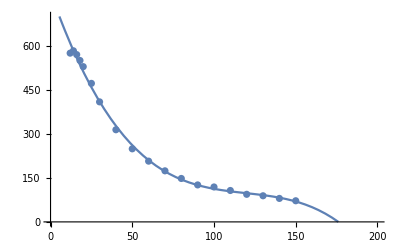

```mathematica
Show[plotLine,plotData]
```

```mathematica
serial=DeviceOpen["Serial",{"/dev/ttyUSB1","BaudRate"->19200}]
```

General::cdir: Cannot set current directory to .dbus.

DeviceObject[…]

```mathematica
DeviceReadBuffer[serial,50]
```

{10,83,116,97,114,116,105,110,103,32,83,101,116,117,112,13,10,57,48,44,57,48,44,54,55,13,10,45,50,51,44,49,57,44,52,54,13,10,50,51,44,56,44,52,55,55,13,10,45,50}

```mathematica
panTiltDistance[ToExpression[StringSplit[FromCharacterCode[DeviceReadBuffer[serial,"ReadTerminator"->10]],","]]]
```

{10.5,-1.5,24.0867}

```mathematica
panTiltDistance[{-8,1,516}]
```

{-4.5,-3.5,24.7748}

```mathematica
FromCharacterCode[{50,51,52}]
```

234

```mathematica
ToExpression["234"]
```

234

```mathematica
line
```

782.774-15.9408 x+0.128033 x^2-0.000356379 x^3

```mathematica
DeviceReadBuffer[serial,4]
```

{45,55,44,45}

```mathematica
serial["Properties"]
```

{}

```mathematica
DeviceReadLatest[serial]
```

DeviceReadLatest::ncoll: No data was collected for … yet. Try using DeviceRead or a related function first.

DeviceReadLatest[DeviceObject[…]]

```mathematica
DeviceClose[serial]
```

```mathematica
1
```

1

```mathematica
598*5
```

2990